{{RGBColor[1, Rational[77, 255], Rational[148, 255]],Polygon[…]},{RGBColor[1, 1, 0],Triangle[{{0,0},{0,1/2},{1,0}}]},{RGBColor[0, 0, 1],Thickness[0.01],Circle[{0,0},1,{0,π/2}]},{RGBColor[Rational[2, 5], Rational[194, 255], 1],Opacity[0.5],Disk[{0.59103,0.375079},0.3]}}

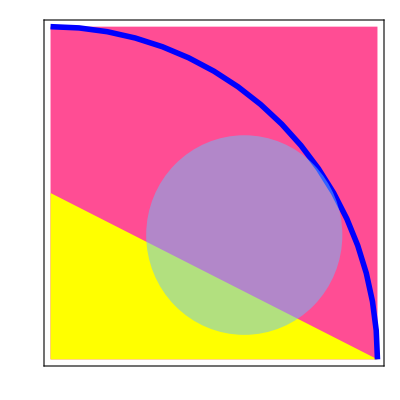
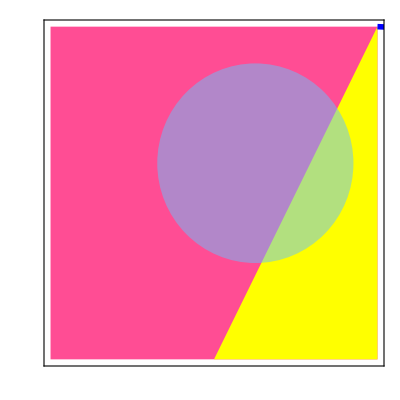
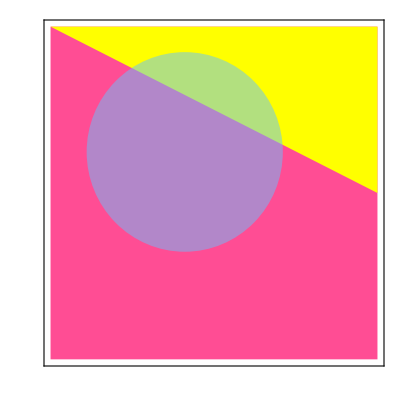
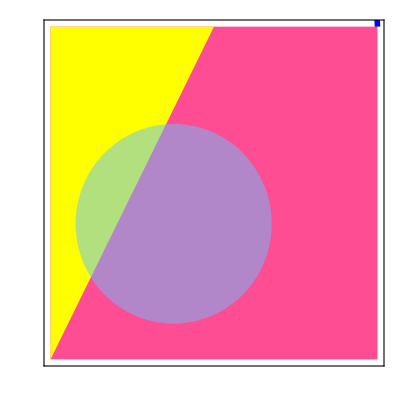
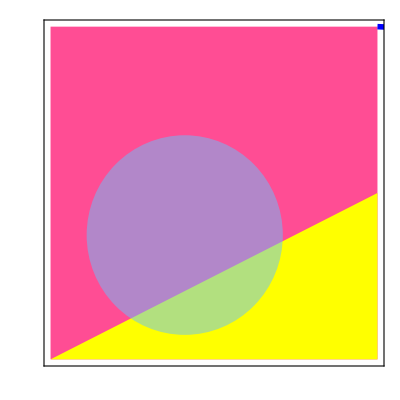
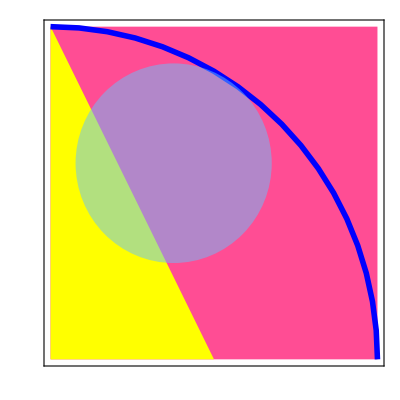
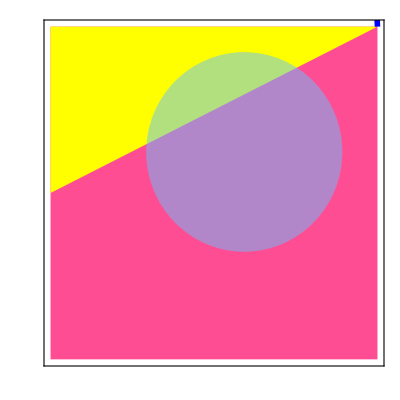
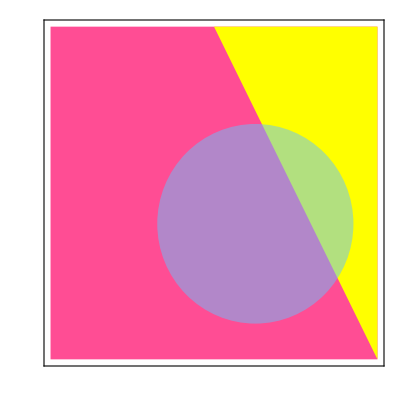
Grid[{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}]

```mathematica
SETTING1by1 = { 
			AspectRatio-> 1,
			PlotRange ->  { {0,1}, {0,1} },

			FrameTicks-> None,
			Frame-> True,
			FrameStyle->Directive[Black,Thickness[0.005]]
                        };

myMotief = {
{RGBColor[255/255,77/255,148/255], Polygon[{{0,0},{0,1},{1,1},{1,0}}]},
{Yellow, Triangle[{{0,0},{0,1/2},{1,0}}]},
{Blue, Thickness[0.01],Circle[ {0,0}, 1, {0, Pi/2} ] },
{RGBColor[102/255,194/255,255/255], Opacity[0.5], Disk[{0.7* Cos[Pi* 0.18],0.7* Sin[Pi * 0.18]}, 0.3]}
}

ori = myMotief;

r9 = GeometricTransformation[ ori ,  RotationTransform[ Pi/2, {1/2,1/2}]  ];
r18 = GeometricTransformation[ ori ,  RotationTransform[ Pi, {1/2,1/2}]  ];
r27  = GeometricTransformation[ ori ,  RotationTransform[ 3 * Pi/2, {1/2,1/2}]  ];

f1 = GeometricTransformation[ori, ReflectionTransform[{1,0},{1/2,1/2}]];
f2 = GeometricTransformation[ori, ReflectionTransform[{-1,1},{1/2,1/2}]];
f3 = GeometricTransformation[ori, ReflectionTransform[{0,-1},{1/2,1/2}]];
f4 = GeometricTransformation[ori, ReflectionTransform[{1,1},{1/2,1/2}]];
Grid[{Graphics[ori,SETTING1by1]}, 
{Graphics[r9,SETTING1by1]},
{Graphics[r18,SETTING1by1]},
{Graphics[r27,SETTING1by1]},
{Graphics[f1,SETTING1by1]},
{Graphics[f2,SETTING1by1]},
{Graphics[f3,SETTING1by1]},
{Graphics[f4,SETTING1by1]}]
```

```mathematica
makeSuperTile[{x_, y_, u_, v_}] :={ 
									GeometricTransformation[x, TranslationTransform[ {0,1}]], 
									GeometricTransformation[y, TranslationTransform[ {1,1}]],
									GeometricTransformation[u, TranslationTransform[ {1,0}]], 
									GeometricTransformation[v, TranslationTransform[ {0,0}]] 
								}
```

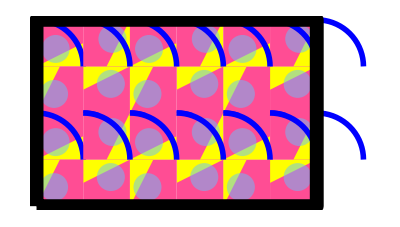

```mathematica
superTile = makeSuperTile[ { f1, r9, f3, r27} ];
Graphics[{
		    Table[
			GeometricTransformation[superTile, TranslationTransform[{2 *x,2 *y}]],
				{x,0,2}, {y,0, 1}
			],

		Thickness[0.025], Black, Line[{ {0,0}, {6,0}, {6,4}, { 0,4}, {0,0} } ]
               }
                  ]
```

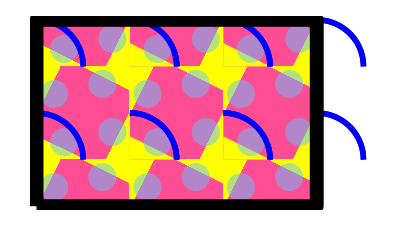

```mathematica
superTile = makeSuperTile[ { ori, r9, r18, r27} ];
Graphics[{
		    Table[
			GeometricTransformation[superTile, TranslationTransform[{2 *x,2 *y}]],
				{x,0,2}, {y,0, 1}
			],

		Thickness[0.025], Black, Line[{ {0,0}, {6,0}, {6,4}, { 0,4}, {0,0} } ]
               }
                  ]
```

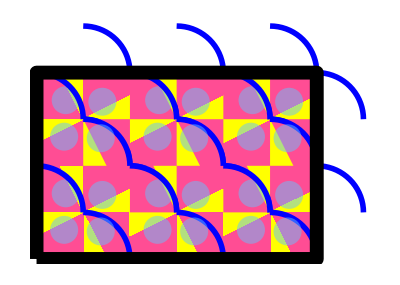

```mathematica
superTile = makeSuperTile[ { f4,f1, f2, f3} ];
Graphics[{
		    Table[
			GeometricTransformation[superTile, TranslationTransform[{2 *x,2 *y}]],
				{x,0,2}, {y,0, 1}
			],

		Thickness[0.025], Black, Line[{ {0,0}, {6,0}, {6,4}, { 0,4}, {0,0} } ]
               }
                  ]
```